```mathematica
lines= {RandomReal[],RandomReal[],2Pi RandomReal[]}&/@Range[10]
```

{{0.41816,0.921857,3.29772},{0.180902,0.506966,0.0513252},{0.799031,0.795428,5.40042},{0.801817,0.837024,0.0163583},{0.291826,0.524299,0.129433},{0.570647,0.511232,0.211703},{0.897766,0.367342,2.63074},{0.91945,0.145655,0.946555},{0.585231,0.737545,4.43627},{0.520804,0.698861,4.29444}}

```mathematica
vecs={Cos[#[[3]]],Sin[#[[3]]]}&/@lines
```

{{-0.987837,-0.155493},{0.998683,0.0513026},{0.635021,-0.772495},{0.999866,0.0163576},{0.991635,0.129072},{0.977674,0.210125},{-0.872327,0.488922},{0.584482,0.811407},{-0.272627,-0.96212},{-0.405891,-0.913921}}

```mathematica
above[{x_,y_}]:=Product[Sign[vecs[[i]].{x-lines[[i,1]],y-lines[[i,2]]}],{i,1,Length[lines]}]
```

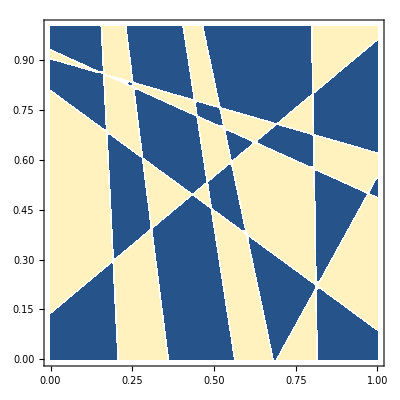

```mathematica
ContourPlot[above[{x,y}],{x,0,1},{y,0,1}]
```

```mathematica
?Product
```

Product[f,{i,i_max}] evaluates the product ∏_(i=1)^i_max f. 
Product[f,{i,i_min,i_max}] starts with i=i_min. 
Product[f,{i,i_min,i_max,di}] uses steps di. 
Product[f,{i,{i_1,i_2,…}}] uses successive values i_1, i_2, ….
Product[f,{i,i_min,i_max},{j,j_min,j_max},…] evaluates the multiple product ∏_(i=i_min)^i_max ∏_(j=j_min)^j_max … f. 
Product[f,i] gives the indefinite product ∏_i f.